# Ramification Singularity

A polynomial homotopy h:ℂ^n×ℂ→ℂ^n for a polynomial p:ℂ^n→ℂ^n is a smooth function with h(z,0)=p(z) 
and h(z,1) a simple polynomial system with at least as many roots as p(z)=0.   The homotopy ODE
(ODE)	A(z,a).z'(t)=-∂_a h(z,a)a'[t]
with A(z,a)=∇h(z,a) comes from differentiating h(z(t),a(t))=0. Paths can cross if Det(A(z,a))=0. These are called ramification points.  Near ramification points the condition number of A is large and care is required when solving the ODE for z'.

In our randomized systems the null space at a ramification point is “almost surely” one dimensional.  This is the technical term
https://en.wikipedia.org/wiki/Almost_surely for with probability one.  The behavior near a generic ramification point follows from an SVD based argument.  I am going to shift the ramification point to z=0 and a=0 and write
	A(z,0)=U(z,a).(σ_1(z,a) |   | □ | □ |  
  | σ_2(z,a) | □ | □ |  
□ | □ | □ | □ | □
□ | □ | □ | □ | □
□ | □ | □ | □ | b.z+a).V_0(z,a)ᵀ

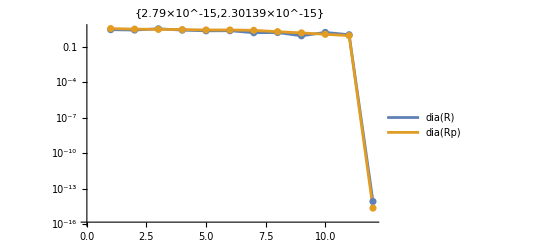

```mathematica
m=12;
A=RandomComplex[{-1-I,1+I},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
{uMin,sMin,vMin}={U⟦All,m⟧,S⟦m,m⟧,V⟦All,m⟧};
ϵ=10^-14;
A=A-(1-ϵ)sMin KroneckerProduct[uMin,Conjugate[vMin]];
{Q,R}=QRDecomposition[A];Q=ConjugateTranspose[Q];
{Qp,Rp,P}=QRDecomposition[A,Pivoting->True];Qp=ConjugateTranspose[Qp];
{Map[ Min,Abs[{Diagonal[R], Diagonal[Rp]}]],
Abs[{R⟦m,m⟧,Rp⟦m,m⟧}]};
MatrixPlot[P];
ListLogPlot[{Abs[Diagonal[R]],Abs[Diagonal[Rp]]},Joined->True,Mesh->All,
PlotLabel->Map[Norm,{A-Q.R,A.P-Qp.Rp}],
PlotLegends->{"dia(R)","dia(Rp)"}]
```

```mathematica
Diagonal[R]
```

{3.06+0. ⅈ,2.92282+0. ⅈ,2.15346+0. ⅈ,-2.87106+0. ⅈ,-1.64353+0. ⅈ,-1.88516+0. ⅈ,-1.79789+0. ⅈ,-1.79325+0. ⅈ,-1.71984+0. ⅈ,0.787222+0. ⅈ,0.952888+0. ⅈ,9.86843×10^-15+0. ⅈ}

```mathematica
Map[Norm,{Q⟦All,-1⟧,vMin}]
```

{1.,1.}

```mathematica
Diagonal[R]
```

{-2.97864+0. ⅈ,-2.86461+0. ⅈ,-2.73951+0. ⅈ,-1.9023+0. ⅈ,2.67275+0. ⅈ,-2.03868+0. ⅈ,-1.51046+0. ⅈ,-1.08853+0. ⅈ,1.36466+0. ⅈ,0.615461+0. ⅈ,1.32171+0. ⅈ,3.83407×10^-12+0. ⅈ}

```mathematica
?QRDecomposition
```

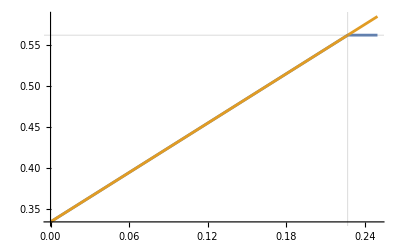

```mathematica
m=12;
A=RandomComplex[{-1-I,1+I},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
{uMin,sMin,vMin}={U⟦All,m⟧,S⟦m,m⟧,V⟦All,m⟧};
sPMin=S⟦m-1,m-1⟧;
f[α_]:= SingularValueList[A+α KroneckerProduct[uMin,Conjugate[vMin]]]
Plot[ {f[α]⟦m⟧,sMin+α},{α, 0,1.1(sPMin-sMin)},
GridLines->{{sPMin-sMin},Diagonal[S]},
PlotRange->All]
```

Log[t+ⅈ α]-Log[ⅈ α]

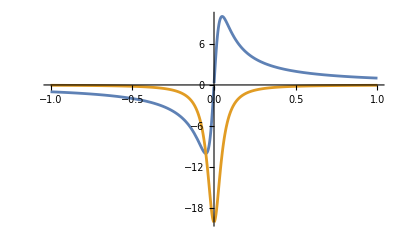

```mathematica
f[α_,t_]:=1/(t+I α)
Integrate[f[α,τ],{τ,0,t},Assumptions->{α>0,t>0}]
Plot[{
Re[f[0.05,t]],Im[f[0.05,t]]
},{t,-1,1},PlotRange->All]
```